```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

#### Using number of points that are n steps away to figure dimension:

```mathematica
Prepend[Table[{n,Mod[n,2]+1},{n,0,8}],{"# steps","# pts"}]//Grid
```

# steps | # pts
0 | 1
1 | 2
2 | 1
3 | 2
4 | 1
5 | 2
6 | 1
7 | 2
8 | 1

```mathematica
Table[{n,Mod[n,2]+1},{n,0,8}]
```

{{0,1},{1,2},{2,1},{3,2},{4,1},{5,2},{6,1},{7,2},{8,1}}

```mathematica
Last/@%
```

{1,2,1,2,1,2,1,2,1}

Differences are like discrete derivatives. A 3-dimensional object has a 3-dimensional volume and a 2-dimensional boundary.  Take 3 derivatives to reach a constant.

```mathematica
D[4/3 π r^3,r]
```

4 π r^2

```mathematica
D[%,r]
```

8 π r

```mathematica
D[%,r]
```

8 π

Here’s the interior of our example network:

```mathematica
Accumulate[{1,2,1,2,1,2,1,2,1}]
```

{1,3,4,6,7,9,10,12,13}

Here’s the series of growing “boundaries”, and it’s already a “constant” row:

```mathematica
Differences[%]
```

{2,1,2,1,2,1,2,1}

#### A wider band

```mathematica
rs01=FromReducedRankRuleSet[{"AAB"->"ABA",""->"A"}]
```

<|Index→393148,QCode→33423431,RuleSet→{AAB→ABA,→A}|>



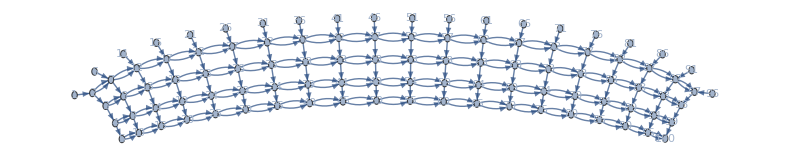
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss01=SSS[rs01,"ABABABABA",100,SSSMax->25,SSSSize->75,NetSize->600];
```

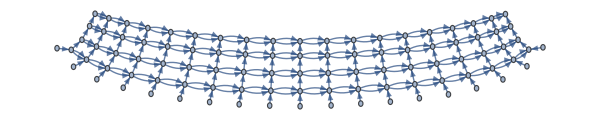
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss01,SSSMax->25,SSSSize->75,NetMax->95,NetSize->600,VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
SSSInteractiveDisplay[sss01]
```

```mathematica
data=sss01[["Distance"]]
```

{0,1,2,3,4,∞,2,3,4,5,∞,3,4,5,6,∞,4,5,6,7,∞,5,6,7,8,∞,6,7,8,9,∞,7,8,9,10,∞,8,9,10,11,∞,9,10,11,12,∞,10,11,12,13,∞,11,12,13,14,∞,12,13,14,15,∞,13,14,15,16,∞,14,15,16,17,∞,15,16,17,18,∞,16,17,18,19,∞,17,18,19,20,∞,18,19,20,21,∞,19,20,21,22,∞,20,21,22,23}

```mathematica
Differences[data]
```

{1,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1,∞,-∞,1,1,1}

Taking Differences once gave us a constant: This network is 1-dimensional.

Another way to get at the same result is to look at the patterns in RulesUsed:

```mathematica
sss01["RulesUsed"]
```

{2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1}

Clumping by 5 at a time, that’s a constant.  (This method assumes 1 difference has already been effectively taken.)

#### Another example

```mathematica
rs02=FromReducedRankRuleSet[{"A"->"B","BB"->"",""->"AA"}]
```

<|Index→325635,QCode→24243403,RuleSet→{A→B,BB→,→AA}|>


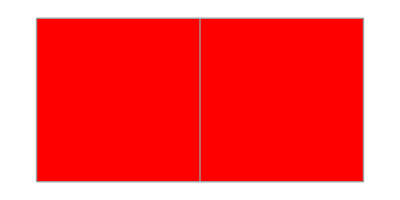
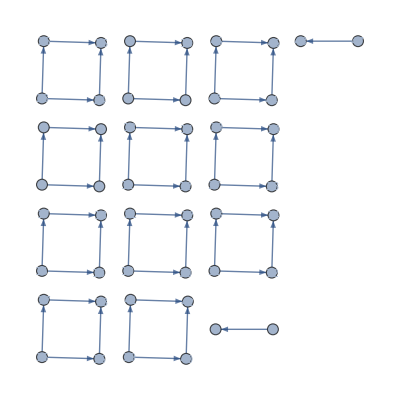
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss02=SSS[rs02,"ABC",50,SSSMax->25,SSSSize->25,NetMax->48,NetSize->400];
```

We can’t use “Distance” is a way to talk about dimension, since most vertices are unreachable from the origin:

```mathematica
data=sss02[["Distance"]]
```

{0,1,1,2,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

We can’t use “Distance” is a way to talk about dimension, since most vertices are unreachable from the origin:

```mathematica
$SSSRulesUsed
```

{1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2,3,1,1,2}

Clumping by 4 at a time, it’s a constant: The network counts as 1-dimensional.